```mathematica
a=1;
J=1;
S=1;
Δ=0.01;
B=0.00;
d=0.001;
```

```mathematica
f[kx_,ky_]:=4*J*S+2*S*Δ+B
r1[kx_,ky_]:=2*J*S*(Cos[kx*a]+Cos[ky*a])
r2[kx_,ky_]:=2*d*S*(Cos[kx*a]-Cos[ky*a])
h[kx_,ky_]:=4*J*S+2*S*Δ-B
```

```mathematica
ω[kx_,ky_]:=0.5*Sqrt[(f[kx,ky]+h[kx,ky])^2-4*(r1[kx,ky]*r1[kx,ky]+r2[kx,ky]*r2[kx,ky])]
δ[kx_,ky_]:=0.5*(f[kx,ky]-h[kx,ky])
```

```mathematica
Eα[kx_,ky_]:=ω[kx,ky]+δ[kx,ky]
Eβ[kx_,ky_]:=ω[kx,ky]-δ[kx,ky]
```

```mathematica
Plot3D[{Eα[kx,ky],-Eβ[kx,ky]},{kx,-π/a,π/a},{ky,-π/a,π/a},
RegionFunction->Function[{kx,ky},ky<-kx+π/a&&ky>-kx-π/a&&ky>kx-π/a&&ky<kx+π/a],
AxesLabel->{Style["ak_x",Bold,25],Style["ak_y",Bold,20],Style["E/SJ",Bold,20]},
PlotStyle->{Red,Lightblue,Thick},
ImageSize->Large,
Ticks->{{-Pi/a,0,Pi/a},{-Pi/a,0,Pi/a},{-6,-3,0,3,6}},
AxesStyle->Directive[Black,20],
PlotTheme->"Scientific",
Boxed->False,
PlotPoints->50]
```

-Graphics3D-

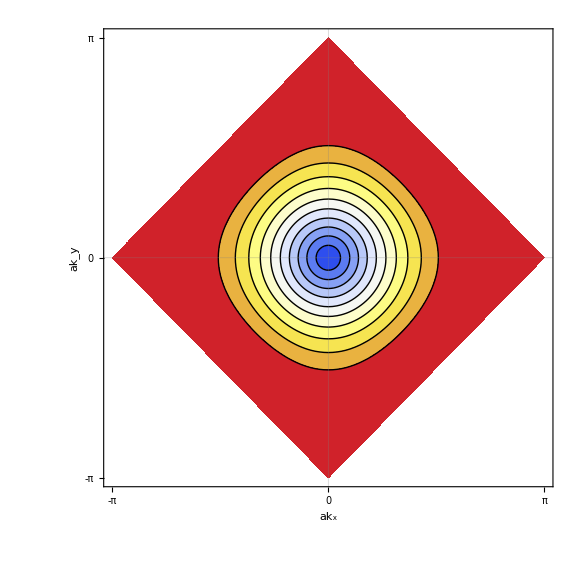

```mathematica
ContourPlot[Eα[kx,ky],{kx,-π/a,π/a},{ky,-π/a,π/a},
RegionFunction->Function[{kx,ky},ky<-kx+π/a&&ky>-kx-π/a&&ky>kx-π/a&&ky<kx+π/a],
ColorFunction->"TemperatureMap",
PlotPoints->50,
ImageSize->Large,
PlotRange->Full,
Contours->10,
Axes->True,
AxesLabel->{Style["ak_x",Bold,20],Style["ak_y",Bold,20]},
FrameTicks->{{-Pi/a,0,Pi/a},{-Pi/a,0,Pi/a}},
LabelStyle->{20,Black},
PlotTheme->"Scientific"]
```

```mathematica
ϕ[kx_,ky_]:=ArcTan[r2[kx,ky]/r1[kx,ky]]
θ[kx_,ky_]:=ArcCosh[(f[kx, ky]+h[kx,ky])/(2*ω[kx,ky])]
```

```mathematica
F=0.5*Sinh[θ[kx,ky]]*(D[θ[kx,ky],kx]*D[ϕ[kx,ky],ky]-D[θ[kx,ky],ky]*D[ϕ[kx,ky],kx]);
F/.{kx->2,ky->1};
F/.{kx->-2,ky->-1};
```

```mathematica
Plot3D[F,{kx,-π/a,π/a},{ky,-π/a,π/a},
RegionFunction->Function[{kx,ky},ky<-kx+π/a&&ky>-kx-π/a&&ky>kx-π/a&&ky<kx+π/a],
AxesLabel->{Style["ak_x",Bold,20],Style["ak_y",Bold,20],Style["(F^α)_xy",Bold,20]},
Ticks->{{-Pi/a,0,Pi/a},{-Pi/a,0,Pi/a},{0.0005,0,-0.0005}},
ColorFunction->"TemperatureMap",
PlotPoints->50,
ImageSize->Large,
PlotRange->Full,
AxesStyle->Directive[Black,20],
PlotTheme->"Scientific"]
```

-Graphics3D-

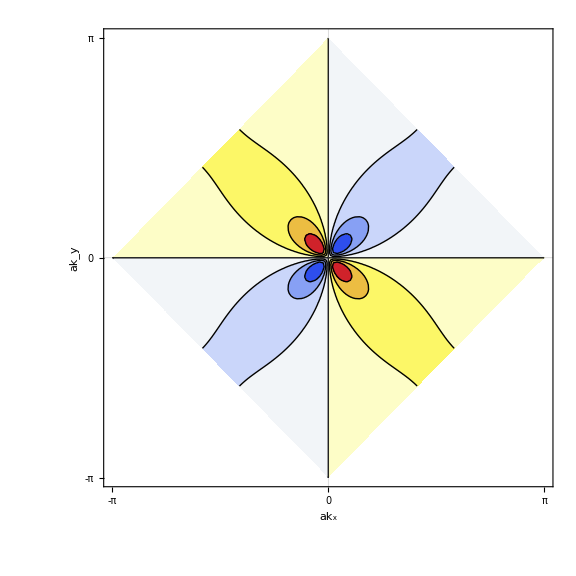

```mathematica
ContourPlot[F,{kx,-π/a,π/a},{ky,-π/a,π/a},
RegionFunction->Function[{kx,ky},ky<-kx+π/a&&ky>-kx-π/a&&ky>kx-π/a&&ky<kx+π/a],
ColorFunction->"TemperatureMap",
PlotPoints->50,
ImageSize->Large,
PlotRange->Full,
Contours->7,
Axes->True,
AxesLabel->{Style["ak_x",Bold,20],Style["ak_y",Bold,20]},
FrameTicks->{{-Pi/a,0,Pi/a},{-Pi/a,0,Pi/a}},
LabelStyle->{20,Black},
PlotTheme->"Scientific"]
```

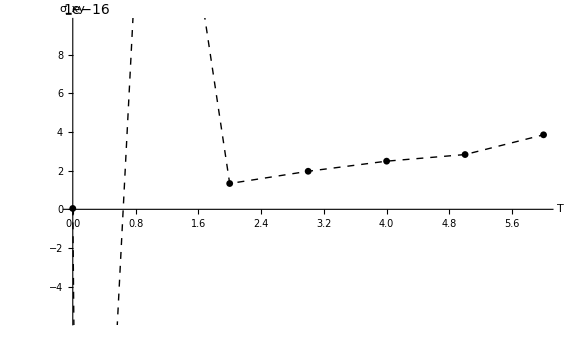

```mathematica
σ[T_]:=NIntegrate[-F[kx,ky]*(Coth[Eα[kx,ky]/(2*T)]+Coth[Eβ[kx,ky]/(2*T)]),{kx,0,2π/a},{ky,0,π/a}]
DiscretePlot[σ[T],{T,{0.000001,0.1,1,2,3,4,5,6}},
Filling->None,AxesLabel->{Style["T",Bold,20],Style["σ_xy",Bold,20]},Joined->True,PlotMarkers->{Automatic,7},PlotStyle->{Black,Dashed,Thick},ImageSize->Large]
```

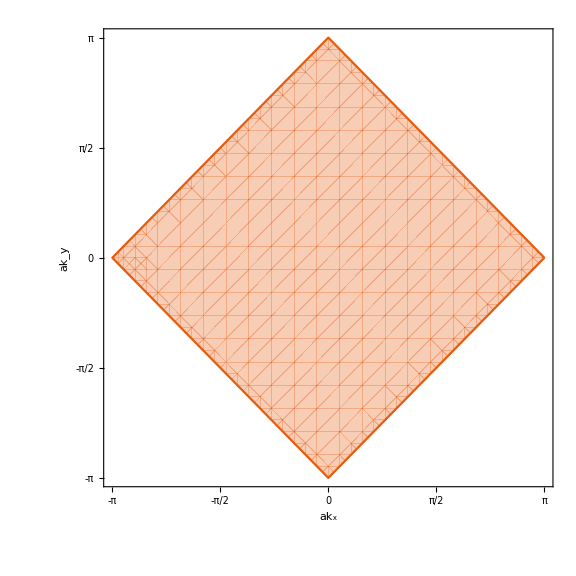

```mathematica
p=RegionPlot[ky<-kx+π/a&&ky>-kx-π/a&&ky>kx-π/a&&ky<kx+π/a,
{kx,-π/a,π/a},{ky,-π/a,π/a},
ImageSize->Large,
Axes->True,
AxesLabel->{Style["ak_x",Bold,20],Style["ak_y",Bold,20]},
FrameTicks->{{-Pi/a,-Pi/2a,0,Pi/2a,Pi/a},{-Pi/2a,-Pi/a,0,Pi/2a,Pi/a}},
LabelStyle->{20,Black},
PlotTheme->"Scientific",
GridLines->{{π/2a,-π/2a},{-π/2a,π/2a}}]
```

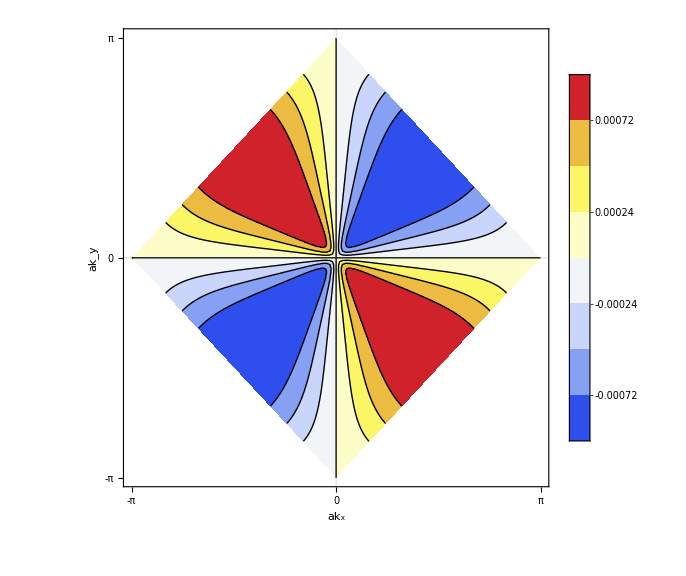

```mathematica
ContourPlot[F*Eα[kx,ky],{kx,-π/a,π/a},{ky,-π/a,π/a},
RegionFunction->Function[{kx,ky},ky<-kx+π/a&&ky>-kx-π/a&&ky>kx-π/a&&ky<kx+π/a],
PlotPoints->50,
ImageSize->Large,
ColorFunction->"TemperatureMap",
PlotRange->Full,
Contours->7,
Axes->True,
AxesLabel->{Style["ak_x",Bold,20],Style["ak_y",Bold,20]},
FrameTicks->{{-Pi/a,0,Pi/a},{-Pi/a,0,Pi/a}},
LabelStyle->{20,Black},
PlotTheme->"Scientific",
PlotLegends->Automatic]
```